```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
ClearSystemCache[];
```

```mathematica
b1=Interpolation[Import[NotebookDirectory[]<>"points_b1f.m"]];
b1gauss=Interpolation[Import[NotebookDirectory[]<>"brute_force_points_b1f.m"]];
b1gausspoints=Import[NotebookDirectory[]<>"brute_force_points_b1f.m"];
```

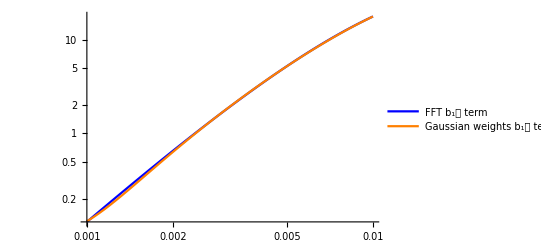

```mathematica
plot=LogLogPlot[{Re[b1[k]/2]//Abs,Re[b1gauss[k]]//Abs},{k,0.001,0.01},PlotLegends->{"FFT b_1𝒻 term","Gaussian weights b_1𝒻 term"},PlotStyle->{Directive[Blue],Directive[Orange]}]
```

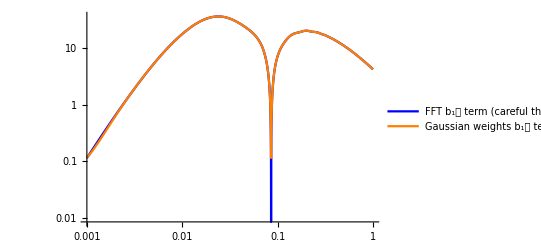

```mathematica
plot=LogLogPlot[{Re[b1[k]/2]//Abs,Re[b1gauss[k]]//Abs},{k,0.001,1},PlotLegends->{"FFT b_1𝒻 term (careful that I do not multiply by 𝒻/2 when computing its FFT)","Gaussian weights b_1𝒻 term, with 𝒻/2"},PlotStyle->{Directive[Blue],Directive[Orange]}]
```

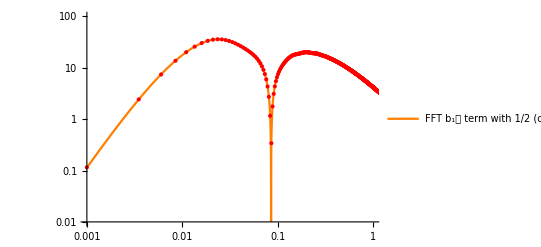

```mathematica
plot=Show[{LogLogPlot[{Re[b1[k]/2]//Abs},{k,0.001,1},PlotLegends->{"FFT b_1𝒻 term with 1/2 (careful that I do not multiply by 𝒻/2 when computing its FFT matrix)"},PlotStyle->{Directive[Blue],Directive[Orange]},PlotRange->{{0.001,1},{0.01,100}},PlotPoints->200],ListLogLogPlot[b1gausspoints//Abs,PlotStyle->{Red}]}]
```

```mathematica
Export[NotebookDirectory[]<>"comparison_plot_b1f.pdf",plot];
```